```mathematica
alber={1->2,2->3, 3->4};
```

```mathematica
Dynamic[TreePlot[alber,VertexLabeling->True], UpdateInterval-> 0]
```

```mathematica
{PopupMenu[Dynamic[root],{1,2,3}],Dynamic[root]}
{PopupMenu[Dynamic[left],{1,2,3}],Dynamic[left]}
{PopupMenu[Dynamic[right],{1,2,3}],Dynamic[right]}
```

{,}

{,}

{,}

2

1

3

```mathematica
Print[root]
```

2

```mathematica
Dynamic[g={root->left, root->right}, UpdateInterval->0]
```

```mathematica
{Root->left,root->right}
```

```mathematica
AppendTo[g, right-> 4]
```

{1→2,1→3,3→4}

```mathematica
TreePlot[{41-> 38, 38-> 31},VertexLabeling->True]
```

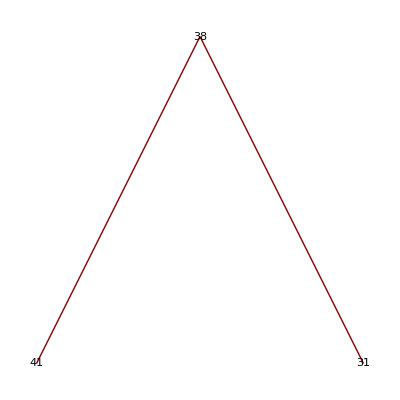

TEST:

La radice di un albero deve essere di colore?

```mathematica
x="";
{"Nero"RadioButton[Dynamic[x],"Giusto"],"Rosso"RadioButton[Dynamic[x],"Sbagliato"]}
Dynamic[x]
```

{Nero ,Rosso }

I nodi NIL devono essere di colore ROSSO?

```mathematica
y="";
{"Vero"RadioButton[Dynamic[y],"Sbagliato"],"Falso"RadioButton[Dynamic[y],"Giusto"]}
Dynamic[y]
```

{Vero ,Falso }

Se un nodo è rosso, allora entrambi i suoi figli sono neri?

```mathematica
f="";
{"Vero"RadioButton[Dynamic[f],"Giusto"],"Falso"RadioButton[Dynamic[f],"Sbagliato"]}
Dynamic[f]
```

{Vero ,Falso }

figura 1:

L’albero in figura 1 é bilanciato?

```mathematica
z="";
{"Vero"RadioButton[Dynamic[z],"Sbagliato"],"Falso"RadioButton[Dynamic[z],"Giusto"]}
Dynamic[z]
```

{Vero ,Falso }

Sempre in riferimento alla figura 1, in che tipo di caso di rotazione mi trovo?

```mathematica
w="";
{"1"RadioButton[Dynamic[w],"Giusto"],"2"RadioButton[Dynamic[w],"Sbagliato, non é il 2"],"3"RadioButton[Dynamic[w],"Sbagliato, non é il 3"],"4"RadioButton[Dynamic[w],"Sbagliato, non é il 4"]}
Dynamic[w]
```

{1 ,2 ,3 ,4 }